```mathematica
DSolve[f''[x]==f[x]^2,f,x]
```

{{f→Function[{x},6^(1/3) WeierstrassP[(x+C[1])/6^(1/3),{0,C[2]}]]}}

```mathematica
ClearAll[f]
eq=α f'''[x]-β f[x]f'[x](*+f'[x]*)
```

-β f[x] f'[x]+α f^(3)[x]

```mathematica
f[x_]=A WeierstrassP[B x+F,{g2,g3}];
```

```mathematica
eq//Simplify
```

A B (12 B^2 α-A β) WeierstrassP[F+B x,{g2,g3}] WeierstrassPPrime[F+B x,{g2,g3}]

```mathematica
B=Solve[12 B^2 α-A β==0,B]⟦2,1,2⟧
```

(√A √β)/(2 √3 √α)

```mathematica
g2=3;
g3=-g2^(3/2)/(3 √3)
```

-1

```mathematica
β=-1;
α=1;
A=-1;
```

```mathematica
f[x]
```

-WeierstrassP[x/(2 √3),{3,-1}]

```mathematica
WeierstrassHalfPeriods[{g2,g3}]
```

{-(ⅈ π)/(√6),∞}

```mathematica
F=-(ⅈ π)/(√6)2 √3
```

-ⅈ √2 π

```mathematica
f[2]
```

-1/2-3/2 Csch[√(3/2) (-1/(√3)-ⅈ √2 π)]^2

```mathematica
Clear[F]
```

```mathematica
F=0
```

0

```mathematica
Re[f[3]]//Simplify
```

1/2 (-1-3 Re[Csch[3/(2 √2)+ⅈ √3 π]^2])

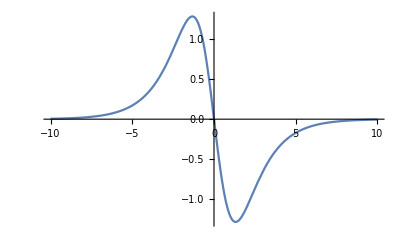

```mathematica
Plot[Im[f[x]],{x,-10,10},PlotRange->Full]
```